```mathematica
Πpar[θ_,u_,mD_]:=mD^2/2((2-2 u^2-u^4 Cos[θ]^2 Sin[θ]^2)/((1-u^2 Sin[θ]^2)^2)-((2+u^2 Sin[θ]^2)(1-u^2)u Cos[θ])/(2(1-u^2 Sin[θ]^2)^(5/2))Log[(u Cos[θ]+√(1-u^2 Sin[θ]^2))/(u Cos[θ]-√(1-u^2 Sin[θ]^2))])
```

```mathematica
Limit[Πpar[θ,u,mD],u->0]
```

mD^2

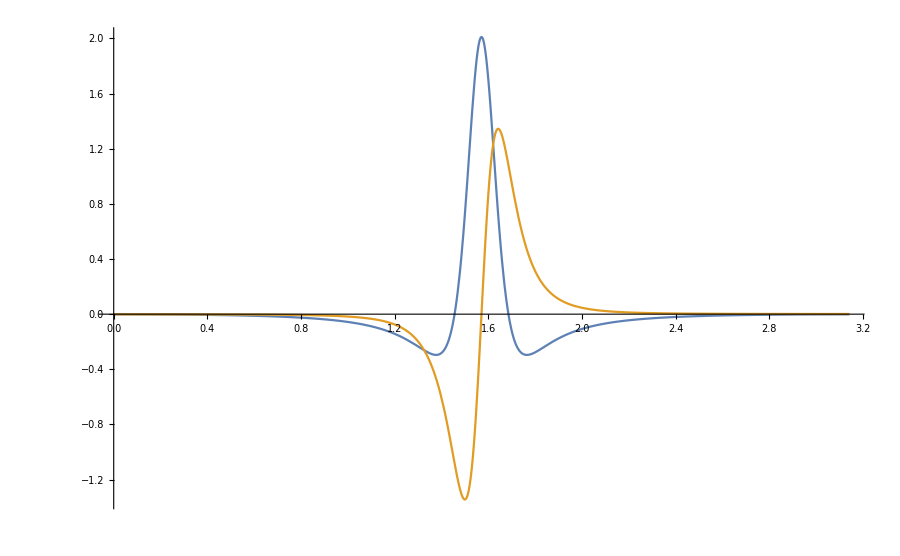

```mathematica
Plot[{Re[Πpar[x,0.99,0.2]],Im[Πpar[x,0.99,0.2]]},{x,0,π},PlotRange->All]
```

```mathematica
Πpar[2,0.9,0.2]
```

0.00527694+0.0952077 ⅈ

```mathematica
Πpar[π-2,0.9,0.2]
```

0.00527694-0.0952077 ⅈ

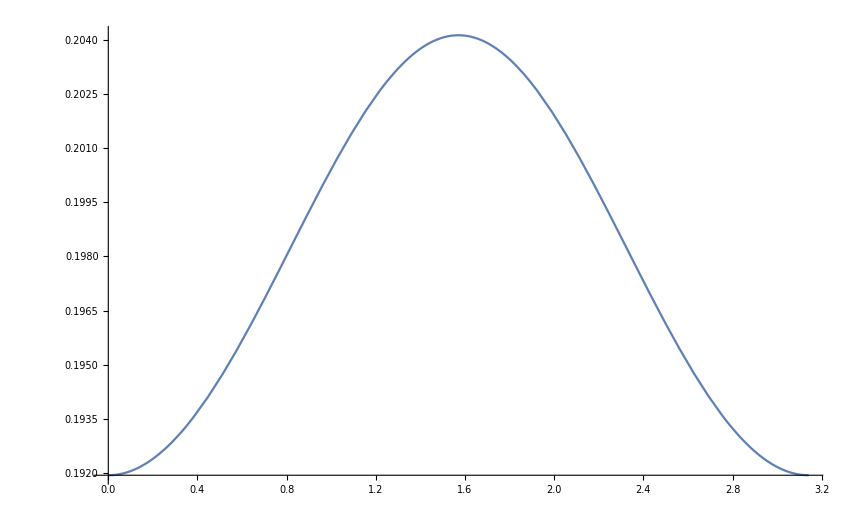

```mathematica
Plot[Re[√Re[Πpar[x,0.2,0.2]]],{x,0,π},PlotRange->All]
```

## Coulomb real

```mathematica
(*Real space permittivity*)
```

```mathematica
Limit[Assuming[{r∈Reals,θ∈Reals,a∈Reals,a>0},Integrate[(p^4 Exp[ⅈ p r Cos[θ]])/(p^2+f[θ])Exp[-a p],{p,0,∞}]],a->0]
```

ConditionalExpression[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 f[θ]]/(2 √π (1/f[θ])^(3/2)),Re[√f[θ]]>0]

```mathematica
MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 f[θ]]/(2 √π (1/f[θ])^(3/2))//TraditionalForm
```

(G_(1,3)^(3,1)(-1/4 r^2 cos^2(θ) f(θ)|-3/2
-3/2,0,1/2))/(2 √π (1/(f(θ)))^(3/2))

```mathematica
Limit[Assuming[{r∈Reals,θ∈Reals,a∈Reals,a>0},Integrate[p^4/(p^2+f[θ])Exp[-a p],{p,0,∞}]],a->0]
```

ConditionalExpression[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},0]/(2 √π (1/f[θ])^(3/2)),Re[√f[θ]]>0]

```mathematica
N[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},10^-10]]
```

8.86227×10^14

```mathematica
MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 f[θ]]/(2 √π (1/f[θ])^(3/2))//Simplify
```

MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Cos[θ]^2 f[θ]]/(2 √π (1/f[θ])^(3/2))

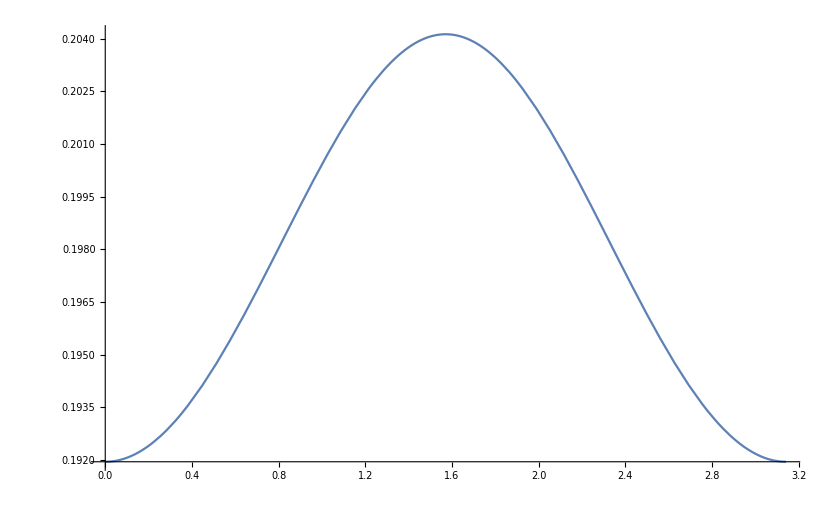

```mathematica
Plot[Re[√Re[Πpar[x,0.2,0.2]]],{x,0,π},PlotRange->All]
```

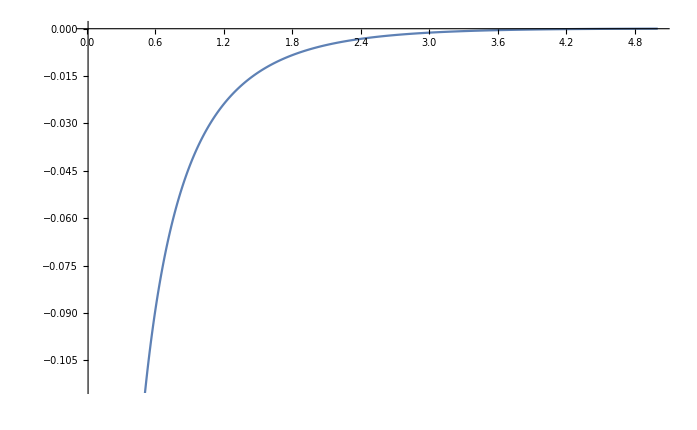

```mathematica
DiscretePlot[ReVcpaper[r/0.197,0.2,0.2,0.5],{r,1/100,5,1/100},Filling->None,Joined->True]
```

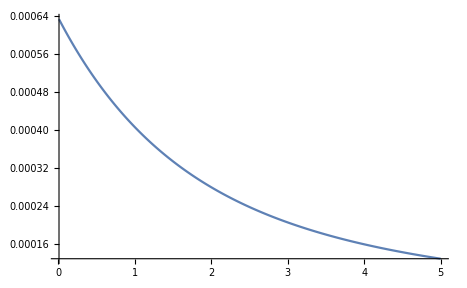

```mathematica
DiscretePlot[1/(4π) NIntegrate[Sin[x] Re[Πpar[x,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[x,0.2,0.2]] r/0.197 Cos[x]],{x,0,π/2}],{r,1/100,5,1/100},Filling->None,Joined->True]
```

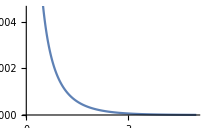

```mathematica
DiscretePlot[checkpaper[r/0.197,0.2,0.2,0.5],{r,1/100,5,1/100},Filling->None,Joined->True]
```

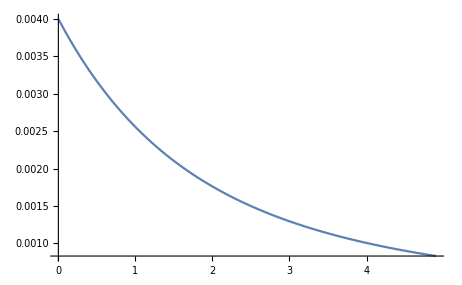

```mathematica
DiscretePlot[check[r/0.197,0.2,0.2,0.5],{r,1/1000,5,1/10},Filling->None,Joined->True]
```

```mathematica
(1/(4π) NIntegrate[Sin[x] Re[Πpar[x,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[x,0.2,0.2]] 0.001/0.197 Cos[x]],{x,0,π/2}]/check[0.001/0.197,0.2,0.2,0.5])^-1
```

1.

```mathematica
(1/(4π) NIntegrate[Sin[x] Re[Πpar[x,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[x,0.2,0.2]] 5/0.197 Cos[x]],{x,0,π/2}]/check[5/0.197,0.2,0.2,0.5])^-1
```

1.

```mathematica
check[10^-50,0.2,0.2,0.5]
```

0.000636937

```mathematica
1/(4π) NIntegrate[Sin[x] Re[Πpar[x,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[x,0.2,0.2]] 0/0.197 Cos[x]],{x,0,π/2}]
```

0.000636937

```mathematica
check[r_,mD_,u_,α_]:=(√π)/(2π)^3 NIntegrate[Sin[θ] Re[Πpar[θ,u,mD]]^(3/2) Re[MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 r^2 Re[Πpar[θ,u,mD]] Cos[θ]^2]],{θ,0,π}];
```

```mathematica
ReVcpaper[r_,mD_,u_,α_]:=-α/r+α NIntegrate[Sin[θ] √Re[Πpar[θ,u,mD]] Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}];
```

```mathematica
ReVcpaper[1,0.2,0.2,0.5]
```

-0.409207

```mathematica
checkpaper[r_,mD_,u_,α_]:=1/(4π)(2/(r/0.197) NIntegrate[Cos[θ]Sin[θ]Re[Πpar[θ,u,mD]]Exp[-√Re[Πpar[θ,u,mD]]r Cos[θ]],{θ,0,π/2}]-NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,u,mD]]^(3/2)Exp[-√Re[Πpar[θ,u,mD]] r/0.197 Cos[θ]],{θ,0,π/2}]);
```

```mathematica
Block[{r=2},NIntegrate[Sin[x] Re[Πpar[x,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[x,0.2,0.2]] r/0.197 Cos[x]],{x,0,π/2}]/NIntegrate[Cos[θ]^2 Sin[θ] Re[Πpar[θ,0.2,0.2]]^(3/2)Exp[-√Re[Πpar[θ,0.2,0.2]] r/0.197 Cos[θ]],{θ,0,π/2}]]
```

5.60434

```mathematica
checkpaper[1,0.2,0.2,0.5]/check[1,0.2,0.2,0.5]
```

4.42964

```mathematica
checkpaper[3,0.2,0.2,0.5]/check[3,0.2,0.2,0.5]
```

1.19734

```mathematica
checkpaper[5,0.2,0.2,0.5]/check[5,0.2,0.2,0.5]
```

0.57511

```mathematica
(*Gauss law solution*)
```

```mathematica
DSolve[f''[r]+2/r f'[r]==(4π √π α)/(2π)^3 Π^(3/2) MeijerG[{{-3/2},{}},{{-3/2,0,1/2},{}},-1/4 Π r^2 y^2],f[r],r]//Simplify
```

{{f[r]→-C[1]/r+C[2]+(α √Π MeijerG[{{-1/2,1},{1/2}},{{-1/2,-1/2,1,3/2},{0}},-1/4 r^2 y^2 Π])/(2 π^(3/2) y^2)}}

## Imaginary parallel part

```mathematica
Assuming[{r∈Reals,x∈Reals},Integrate[(p^3 Exp[ⅈ p r Cos[x]])/((p^2+mD)(p^2+Conjugate[mD])),{p,0,∞}]]
```

ConditionalExpression[1/(2 (mD-Conjugate[mD]))ⅈ (ⅈ mD √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 mD r^2 Cos[x]^2]+mD π Sign[r Cos[x]] (Cosh[√mD Abs[r] Abs[Cos[x]]]-Sinh[√mD Abs[r] Abs[Cos[x]]])+Conjugate[mD] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[mD] Cos[x]^2]+π Sign[r Cos[x]] (-Cosh[Abs[r] Abs[Cos[x]] √Conjugate[mD]]+Sinh[Abs[r] Abs[Cos[x]] √Conjugate[mD]]))),Im[mD]≠0||(Re[mD]≥0&&Re[√mD]>0&&Re[√Conjugate[mD]]>0)]

```mathematica
check[r_,mD_,u_,T_]:=(2 π^2 mD^2 T)/(2π)^3 NIntegrate[((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))Sin[x]/(2 (Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]]))ⅈ (ⅈ Πpar[x,u,mD] √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 Πpar[x,u,mD] r^2 Cos[x]^2]+Πpar[x,u,mD] π Sign[r Cos[x]] (Cosh[√Πpar[x,u,mD] Abs[r] Abs[Cos[x]]]-Sinh[√Πpar[x,u,mD] Abs[r] Abs[Cos[x]]])+Conjugate[Πpar[x,u,mD]] (-ⅈ √π MeijerG[{{-1},{}},{{-1,0},{1/2}},1/4 r^2 Conjugate[Πpar[x,u,mD]] Cos[x]^2]+π Sign[r Cos[x]] (-Cosh[Abs[r] Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]+Sinh[Abs[r] Abs[Cos[x]] √Conjugate[Πpar[x,u,mD]]]))),{x,0,π},WorkingPrecision->20];
```

```mathematica
check[5,2/10,2/10,155/1000]
```

0.00031113478331159373991+0. ⅈ

```mathematica
Block[{r=2,u=0.2,mD=0.2,q=0.5,T=0.155}, q mD^2 T NIntegrate[((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))Sin[x](p^3 Cos[p r Cos[x]])/((p^2+Πpar[x,u,mD])(p^2+Conjugate[Πpar[x,u,mD]])),{p,0,∞},{x,0,π},MaxRecursion->20]]
```

$Aborted

```mathematica
checkpaper[r_,mD_,u_,q_,T_]:=-2 q T NIntegrate[Sin[x]((2+u^2 Sin[x]^2)(1-u^2)^(3/2))/(2(1-u^2 Sin[x]^2)^(5/2))mD^2/(Πpar[x,u,mD]-Conjugate[Πpar[x,u,mD]])(Sinh[√Πpar[x,u,mD] r Cos[x]]SinhIntegral[√Πpar[x,u,mD] r Cos[x]]-Cosh[√Πpar[x,u,mD] r Cos[x]]CoshIntegral[√Πpar[x,u,mD] r Cos[x]]-Sinh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]SinhIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]+Cosh[√Conjugate[Πpar[x,u,mD]] r Cos[x]]CoshIntegral[√Conjugate[Πpar[x,u,mD]] r Cos[x]]),{x,0,π/2}]
```

```mathematica
Re[checkpaper[2,0.2,0.2,0.5,0.155]]
```

0.0711286

```mathematica
inter=Interpolation[Table[{r,Re[checkpaper[r,0.2,0.2,0.5,0.155]]},{r,4.9,5.1,1/1000}]];
```

```mathematica
(inter''[2]+2/2 inter'[2])/(4π 0.5Re[check[2,2/10,2/10,0.155]])
```

-0.965171

```mathematica
(inter''[5]+2/5 inter'[5])/(4π 0.5Re[check[5,2/10,2/10,0.155]])
```

-0.961989